```mathematica
testdata = Accumulate[RandomVariate[NormalDistribution[0,0.5],200]];
```

```mathematica
Get["HPFilter`HPFilter`"]
```

```mathematica
hptest=HPFilter[testdata,1600];
```

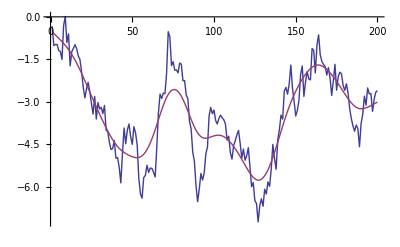

```mathematica
ListLinePlot[{testdata,hptest}]
```

```mathematica
optimalhp=HPFilter[testdata];
```

Eigenvalues::arh: Because finding 200 out of the 200 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

```mathematica
oneside=OneSidedHPFilter[testdata,1600];
```

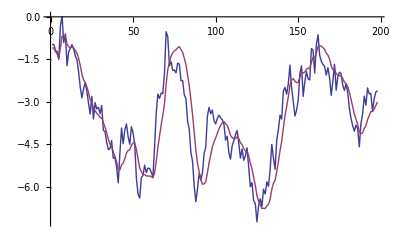

```mathematica
ListLinePlot[{Drop[testdata,2],oneside}]
```

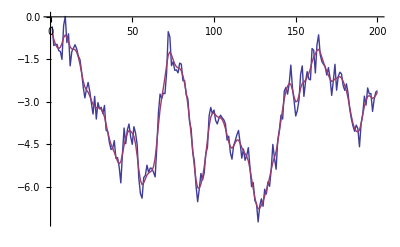

```mathematica
ListLinePlot[{testdata,First@optimalhp}]
```